## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGMd";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data_manuscript.csv";

mainFolder = "fit_PGMd_Keq_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\Manuscript\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(*(626.7176791692085*0.00019)/(417.8117861128057*0.0002)
KeqList0[[1]][[3]]=1.425; (*kcat_f*km_r / kcat_r*km_f*)*)
```

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)


KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 626.718 | 605.827
647.608 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 417.812 | 393.123
442.501 | 1/s | 7 | 37 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMd[c] + 23dpg[c] <=> E_PGMd[c]&23dpg",
				"E_PGMd[c]&23dpg + 3pg[c] <=> E_PGMd[c]&23dpg&3pg",
				"E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg",
				"E_PGMd[c]&23dpg&2pg <=> E_PGMd[c]&23dpg + 2pg[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,Overscript[(PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c, PGMd3],((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PGMd^c&(23dpg)^c&(3pg)^c)_^-((PGMd^c&(23dpg)^c&(2pg)^c)_^)/K_PGMd4) Volume_c k_PGMd4^⟶}

Volume_c (-(PGMd^c&(23dpg)^c&(2pg)^c)_^ k_PGMd4^⟵+(PGMd^c&(23dpg)^c&(3pg)^c)_^ k_PGMd4^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	23dpg[c]	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\haldaneRatio_1.txt"	0.189
1	0.0001	0	0.00002	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.09090909090909091
1	0.0001	0	0.00003169786384922229	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.13680688860321008
1	0.0001	0	0.00005023772863019165	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.2007600089131019
1	0.0001	0	0.00007962143411069939	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.2847472489508013
1	0.0001	0	0.0001261914688960386	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.38686317984685686
1	0.0001	0	0.00020000000000000004	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.5
1	0.0001	0	0.0003169786384922229	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.6131368201531432
1	0.0001	0	0.0005023772863019165	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.7152527510491988
1	0.0001	0	0.0007962143411069948	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.7992399910868982
1	0.0001	0	0.0012619146889603862	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.8631931113967899
1	0.0001	0	0.0020000000000000005	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateFor_3pg.txt"	0.9090909090909091
1	0.0001	0.000018999999999999994	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.09090909090909087
1	0.0001	0.00003011297065676116	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.13680688860321003
1	0.0001	0.00004772584219868205	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.20076000891310186
1	0.0001	0.0000756403624051644	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.2847472489508012
1	0.0001	0.00011988189545123664	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.38686317984685686
1	0.0001	0.00018999999999999996	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.49999999999999994
1	0.0001	0.0003011297065676116	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.6131368201531432
1	0.0001	0.0004772584219868205	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.7152527510491987
1	0.0001	0.0007564036240516448	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.7992399910868982
1	0.0001	0.0011988189545123664	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.8631931113967899
1	0.0001	0.0018999999999999996	0	1	7	30	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\relRateRev_2pg.txt"	0.9090909090909092
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	0	1	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateFor.txt"	626.7176791692085
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057
1	0.0001	1	0	1	7	37	"C:\MASSef\examples\Manuscript\fit_PGMd_Keq_test\input\absRateRev.txt"	417.8117861128057

### Simulate data with uncertainty

```mathematica
nSamples=3;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[1]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10468133456395322
0	0.00008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909086
0	0.00013798244196800728	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860320997
0	0.00021868743295425528	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.0003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.38686317984685675
0	0.0008706103516902622	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.49999999999999983
0	0.001379824419680073	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.6131368201531431
0	0.002186874329542555	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.003465962237659955	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.005493179955794547	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.008706103516902621	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.909090909090909
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	9447.229221055051

### Parameter scan

```mathematica
Export["TPIParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["TPIParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, fitLabel,
						  haldaneRatiosList, KeqList,
 kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

{0.0314694}

No Km or S05 for: {dhap}, therefore the inhibitions affecting these metabolites won't be modeled.

```mathematica
FilePrint[dataPathList[[5]]]
```

dhap[c]	g3p[c]	param_TPI_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0	1	7	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/haldaneRatio_1.txt"	0.10741138560687433
0	0.00010299999999999996	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.09090909090909087
0	0.00016324399882349468	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.13680688860321
0	0.00025872430244548657	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.20076000891310164
0	0.00041005038567010205	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.28474724895080133
0	0.0006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.3868631798468567
0	0.0010299999999999994	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.4999999999999999
0	0.0016324399882349469	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.613136820153143
0	0.0025872430244548686	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7152527510491986
0	0.004100503856701021	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.7992399910868982
0	0.006498860648145985	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.8631931113967899
0	0.010299999999999995	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/relRateRev_g3p.txt"	0.9090909090909091
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.
0	0.01	1	7.6	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit/input/absRateRev.txt"	1.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.914051553689
best_fit: 1.08739549452
best_fit: 1.07779496007
best_fit: 0.946251706542
best_fit: 1.09800519943
best_fit: 1.04918742558
best_fit: 1.09907440924
best_fit: 1.08031038263
best_fit: 0.98128372787
best_fit: 1.03483646544

## Evaluate fit results

```mathematica
(*no uncertainty or parameter scan*)
lmaResultsFileNameNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(*with uncertainty or parameter scan*)
datasetI=2;
lmaResultsFileNameNew=StringTake[lmaResultsFileName,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNameNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | haldaneRatio_1 | 2.44015×10^-7 | 5.95431×10^-14 | 8.00656×10^-7 | 0.0000561864 | 1.425 | 1.425
1 | relRateFor_3pg | 0.0000315855 | 9.97643×10^-10 | 6.61142×10^-6 | 0.00727256 | 0.0909091 | 0.0909025
1 | relRateFor_3pg | 0.0000256054 | 6.55638×10^-10 | 8.06571×10^-6 | 0.00589569 | 0.136807 | 0.136799
1 | relRateFor_3pg | 0.0000172728 | 2.98348×10^-10 | 7.98447×10^-6 | 0.00397712 | 0.20076 | 0.200752
1 | relRateFor_3pg | 6.32955×10^-6 | 4.00632×10^-11 | 4.14997×10^-6 | 0.00145742 | 0.284747 | 0.284743
1 | relRateFor_3pg | 6.97613×10^-6 | 4.86663×10^-11 | 6.21428×10^-6 | 0.00160633 | 0.386863 | 0.386869
1 | relRateFor_3pg | 0.0000217183 | 4.71685×10^-10 | 0.0000250047 | 0.00500095 | 0.5 | 0.500025
1 | relRateFor_3pg | 0.000036461 | 1.3294×10^-9 | 0.0000514778 | 0.0083958 | 0.613137 | 0.613188
1 | relRateFor_3pg | 0.000049768 | 2.47685×10^-9 | 0.0000819691 | 0.0114602 | 0.715253 | 0.715335
1 | relRateFor_3pg | 0.0000607129 | 3.68605×10^-9 | 0.000111739 | 0.0139806 | 0.79924 | 0.799352
1 | relRateFor_3pg | 0.0000690472 | 4.76751×10^-9 | 0.000137247 | 0.0159 | 0.863193 | 0.86333
1 | relRateFor_3pg | 0.0000750286 | 5.6293×10^-9 | 0.000157068 | 0.0172775 | 0.909091 | 0.909248
1 | relRateRev_2pg | 0.0000313143 | 9.80585×10^-10 | 6.55466×10^-6 | 0.00721012 | 0.0909091 | 0.0909025
1 | relRateRev_2pg | 0.0000255672 | 6.53681×10^-10 | 8.05367×10^-6 | 0.00588689 | 0.136807 | 0.136799
1 | relRateRev_2pg | 0.0000175592 | 3.08324×10^-10 | 8.11686×10^-6 | 0.00404306 | 0.20076 | 0.200752
1 | relRateRev_2pg | 7.04229×10^-6 | 4.95938×10^-11 | 4.61727×10^-6 | 0.00162153 | 0.284747 | 0.284743
1 | relRateRev_2pg | 5.745×10^-6 | 3.3005×10^-11 | 5.1176×10^-6 | 0.00132284 | 0.386863 | 0.386868
1 | relRateRev_2pg | 0.0000199128 | 3.9652×10^-10 | 0.000022926 | 0.0045852 | 0.5 | 0.500023
1 | relRateRev_2pg | 0.0000340811 | 1.16152×10^-9 | 0.0000481175 | 0.00784776 | 0.613137 | 0.613185
1 | relRateRev_2pg | 0.0000468696 | 2.19676×10^-9 | 0.0000771951 | 0.0107927 | 0.715253 | 0.71533
1 | relRateRev_2pg | 0.000057388 | 3.29338×10^-9 | 0.000105619 | 0.0132149 | 0.79924 | 0.799346
1 | relRateRev_2pg | 0.0000653976 | 4.27684×10^-9 | 0.000129992 | 0.0150595 | 0.863193 | 0.863323
1 | relRateRev_2pg | 0.0000711459 | 5.06175×10^-9 | 0.000148939 | 0.0163833 | 0.909091 | 0.90924
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateFor | 2.44571×10^-7 | 5.98151×10^-14 | 0.000352934 | 0.0000563146 | 626.718 | 626.718
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812
1 | absRateRev | 2.4403×10^-7 | 5.95508×10^-14 | 0.000234769 | 0.0000561901 | 417.812 | 417.812

### Simulated Data and Best Fit Data Plot

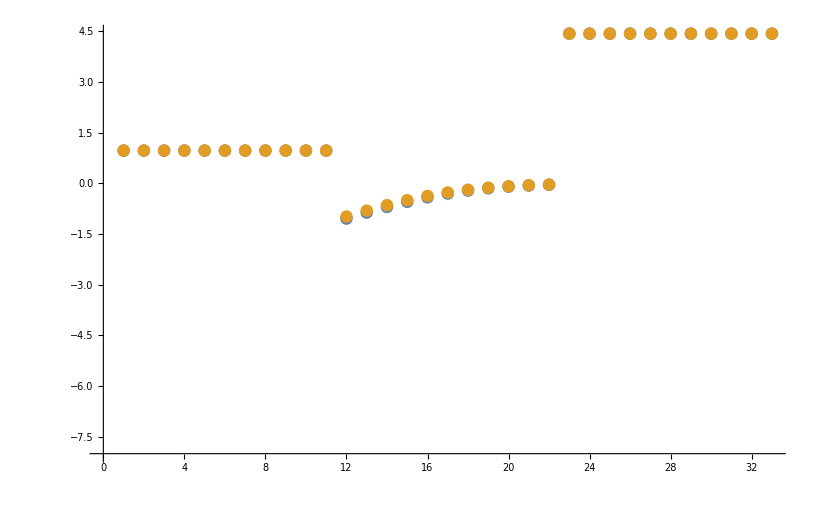

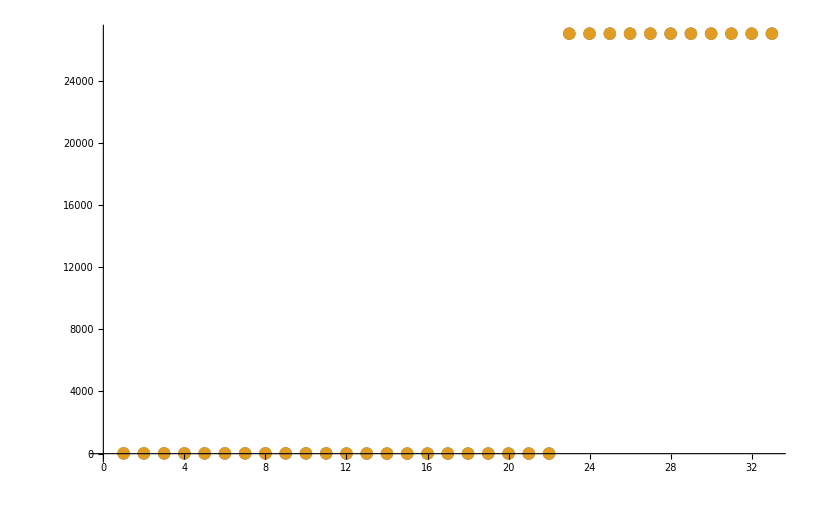

```mathematica
datasetI=40;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

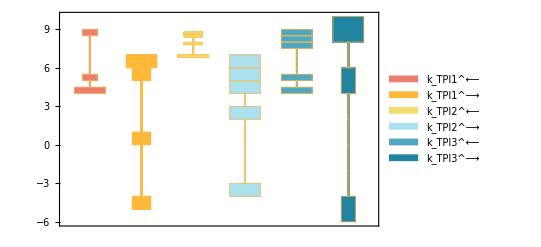

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

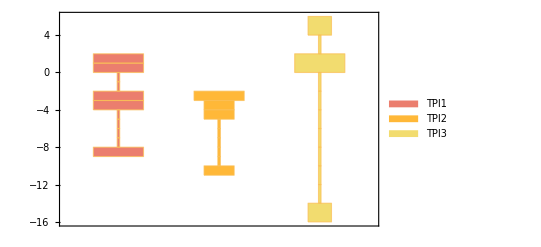

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

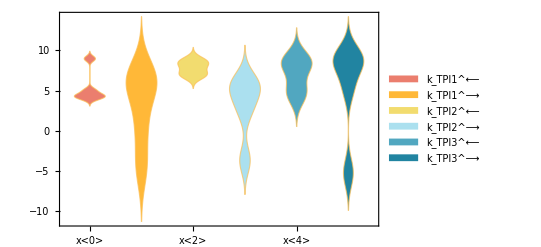

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub,paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.0002 | 0.00019998 | 0.0099994
0.00019 | 0.000189983 | 0.00916823

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
626.718 | 626.718 | 0.0000563146
417.812 | 417.812 | 0.0000561901

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[All,3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
1.425 | 1.425 | 0.0000561864

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

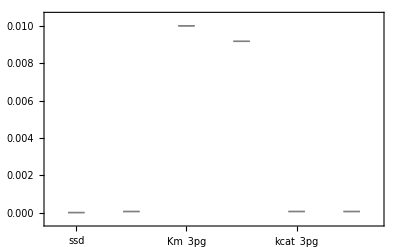

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```